```mathematica
On[Assert]
SetDirectory[NotebookDirectory[]]
<<Tools`
ParallelNeeds["Tools`"](* Import package Tools that define useful functions*)
```

/Users/phuongnguyen/Work/symbiosis_3D_tradeoff

# Graph format

```mathematica
frameStyle = Directive[Black,Thickness[0.003]];
labelStyle = {Black, FontSize-> 24};
colfunctions = "ThermometerColors";
```

# Ecological dynamics of resident

```mathematica
dFdt = ρ F + τ A - α F^2- μ F - β F H; (*Free living parasites*)
dAdt = β H F + p r A - (ν + d)  A - γ(A + H)A; (*Association*)
dHdt = -β H F + r (1 - p)A + r  H - d H - γ(A + H)H; (*Free host*)
```

# Dynamics of mutants and invasion criteria

```mathematica
dFmdt = ρm Fm + τm Am - α F Fm- μ Fm - β Fm H; (*Free living parasites*)
dAmdt = β H Fm + p r Am - (νm + d)  Am - γ(A + H)Am; (*Association*) (*Free host*)
```

```mathematica
Mmat = {{ρm - α F - μ - β H, τm},{β H, r p - νm -d - γ(A + H)}};
Mmat . {Fm, Am} == {dFmdt, dAmdt}//Simplify//Assert
Fmat = {{ρm, τm}, {0, 0}};
Vmat = {{α F + μ + β H, 0}, {-β H, d-r p + νm + γ(A + H) }};
Fmat - Vmat == Mmat//Simplify//Assert
R0 = Eigenvalues[Fmat.Inverse[Vmat]][[2]];
```

```mathematica
ρm/(F α+H β+μ)+(H β τm)/((F α+H β+μ) (d-p r+A γ+H γ+νm))==R0//FullSimplify//Assert
```

## Tradeoff and Invasion surface

```mathematica
𝒪 = θ - v ρ^h + (η ν (ν + d)^g)/νmax; 
ℐ = ((d-p r+(A+H) γ+ν) (F α+H β+μ-ρ))/(H β);
```

## Derivative of the invasion surface

```mathematica
dIdp = D[ℐ, ρ]/.ν-> νpoint;
dIdv = D[ℐ, ν]/.ρ-> ρpoint;
```

# Testing singular strategy

## Tradeoff parameterisation

```mathematica
parstroff = {θ -> 8, η -> 1, v -> 1., d-> 1.3, νmax -> 3};
𝒪/.parstroff
Manipulate[Plot3D[%, {ν, -1, 3}, {ρ, 0, 14}, AxesLabel->Automatic], {g, 0.1, 1.5}, {h, 0.1, 1.5}]
```

8+1/3 ν (1.3+ν)^g-1. ρ^h

## Equilibrium

```mathematica
system = Thread[({dFdt, dAdt, dHdt}/.τ-> 𝒪) ];
```

```mathematica
νeg = -1;
ρeg = 4;
parsTest = { η -> 1., g ->  0.312, μ-> 1.4, α -> 1.2, γ -> 1.23, p-> 0.1, β -> 2.1, r -> 2.3, d -> 1.3, θ -> 8., v -> 1., h-> 1.5, νmax -> 3};
```

```mathematica
NSolvePositive[system,Join[ parsTest, {ν-> νeg, ρ-> ρeg}], τ-> 1, {F, A, H}, equi];
solTest = equi/.%[[1]][[2]]
```

{F→1.09551,A→0.748625,H→0.537586}

## Singular strategy

```mathematica
Show[Plot3D[{𝒪/.parsTest, ℐ/.parsTest/.solTest}, {ν, -1, 3}, {ρ, 0, 4}, AxesLabel->Automatic],
Graphics3D[{Red,PointSize[0.02],Point[{νeg,ρeg,1}]}]]
```

-Graphics3D-

```mathematica
R0troff= R0/.τm -> 𝒪/.ρ -> ρm/.ν -> νm;
```

```mathematica
R0troff/.parsTest/.νm -> νeg/. ρm-> ρeg/.solTest
```

1.

```mathematica
Show[Plot3D[R0troff/.parsTest/.solTest, {νm, -1, 3}, {ρm, 0, 4}, AxesLabel->Automatic, AspectRatio->1], Graphics3D[{Red,PointSize[0.02],Point[{νeg,ρeg,1}]}]]
```

-Graphics3D-

# Scenario 1 of the tradeoff plane: g < 1, h > 1, increase in ν does not cost a lot of energy

```mathematica
par1 = { η -> 1., g ->  0.612, μ-> 1.4, α -> 1.2, γ -> 1.23, p-> 0.1, β -> 2.1, r -> 2.3, d -> 1.3, θ -> 8., v -> 1., h-> 1.5, νmax -> 3};
```

```mathematica
νrange = {-1, 3, 0.6};
ρrange = {0, 4.1, 0.4};
νρlistfull = Flatten[Table[{ν, ρ},{ν, νrange[[1]], νrange[[2]], νrange[[3]]}, {ρ, ρrange[[1]], ρrange[[2]], ρrange[[3]]}], 1];
par1fullresult = Table[NSolveCodim2Positive[system, par1, {ν-> νval}, {ρ-> ρval},νρ, eq, {F, A, H} ], {νval ,νrange[[1]], νrange[[2]], νrange[[3]]},{ρval,ρrange[[1]], ρrange[[2]], ρrange[[3]]}];
par1eq = eq/.Flatten[par1fullresult, 2];

par1νρ = νρ/.Flatten[par1fullresult, 2];
νlist =  par1νρ[[;;, 1]];
ρlist = par1νρ[[;;, 2]];
νlistContourRange =  Thread[{ν, νlist- 0.2, νlist+ 0.2}];
ρlistContourRange = Thread[{ρ, ρlist - 0.2, ρlist + 0.2}];
par1νρextinct = Complement[ νρlistfull, par1νρ];
scale = Round[Max/@Transpose[{Abs[dIdp/.par1/.par1eq/.Thread[νpoint-> νlist]], Abs[dIdv/.par1/.par1eq/.Thread[ρpoint-> ρlist]]}], 0.01];
```

{{τ→1,equi→{F→1.15674,A→0.768957,H→0.526599}}}

{F→1.15674,A→0.768957,H→0.526599}

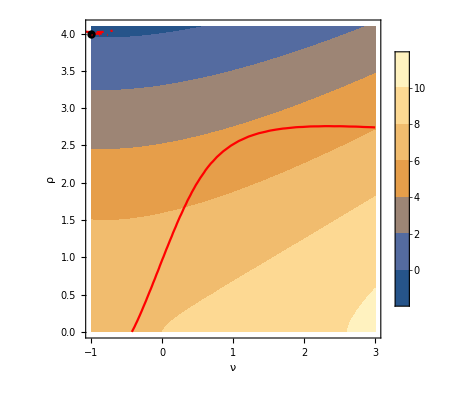

```mathematica
νeg = -1;
ρeg = 4;
NSolvePositive[system, Join[par1, {ν -> νeg, ρ-> ρeg}], τ-> 1,{F, A, H}, equi]
eq1 = equi/.%[[1]][[2]]
Show[ContourPlot[𝒪/.par1, {ν, νrange[[1]], νrange[[2]]}, {ρ,ρrange[[1]], ρrange[[2]]}, FrameLabel->Automatic, ContourStyle -> None,PlotLegends->Automatic],
Graphics[{PointSize[0.015],Point[{νeg, ρeg}]}],
ContourPlot[((ℐ-𝒪)/.par1/.eq1)==0, {ν, -3,3}, {ρ,0,4}, ContourStyle->Red ],
ContourPlot[((ℐ-𝒪)/.par1/.eq1)==0.02 * Round[Max[{Abs[dIdp/.par1/.eq1/.νpoint-> νeg],Abs[dIdv/.par1/.eq1/.ρpoint->ρeg]}], 0.01], {ν, νeg-0.3,νeg+0.3}, {ρ,ρeg -0.5,ρeg + 0.5}, ContourStyle->Directive[Red, Dashed] ],
ContourPlot[((ℐ-𝒪)/.par1/.eq1)==-0.02 * Round[Max[{Abs[dIdp/.par1/.eq1/.νpoint-> νeg],Abs[dIdv/.par1/.eq1/.ρpoint->ρeg]}], 0.01], {ν, νeg-0.3,νeg+0.3}, {ρ,ρeg -0.5,ρeg + 0.5}, ContourStyle->Directive[Red, Dotted] ]]
```

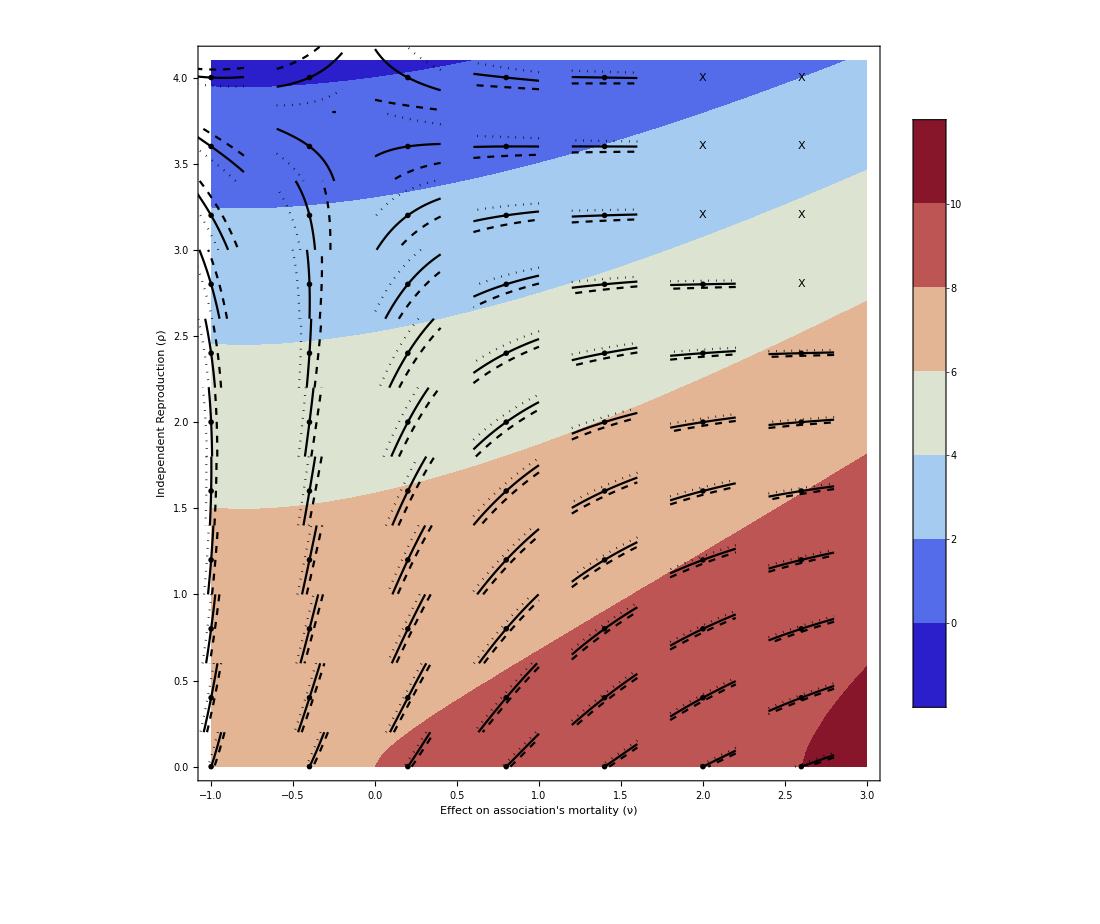

```mathematica
Show[ContourPlot[𝒪/.par1, {ν, νrange[[1]], νrange[[2]]}, {ρ, ρrange[[1]], ρrange[[2]]},Frame-> True, FrameLabel->{ "Effect on association's mortality (ν)","Independent Reproduction (ρ)"}, ColorFunction->colfunctions,ContourStyle -> None,PlotLegends->Automatic, FrameStyle->frameStyle, LabelStyle->labelStyle],MapThread[ContourPlot, {(ℐ-𝒪==0)/.par1/.par1eq, νlistContourRange, ρlistContourRange, ConstantArray[{ ContourStyle->Directive[Black]}, Length[νlistContourRange]]}],
MapThread[ContourPlot, {Thread[((ℐ-𝒪)/.par1/.par1eq)==0.02 * scale], νlistContourRange, ρlistContourRange, ConstantArray[{ ContourStyle->Directive[Black, Dashed]}, Length[νlistContourRange]]}],
MapThread[ContourPlot, {Thread[((ℐ-𝒪)/.par1/.par1eq)==-0.02 * scale], νlistContourRange, ρlistContourRange, ConstantArray[{ ContourStyle->Directive[Black, Dotted]}, Length[νlistContourRange]]}],ListPlot[par1νρ, PlotStyle->Black, PlotMarkers->"OpenMarkers"],ListPlot[par1νρextinct, PlotStyle->Black, PlotMarkers->"X"]]
```

# Scenrio 2 of the tradeoff plane: g < 1, h > 1, increase in ν does not cost a lot of energy

```mathematica
par2 = { η -> 1., g ->  0.312, μ-> 1.4, α -> 1.2, γ -> 1.23, p-> 0.1, β -> 2.1, r -> 2.3, d -> 1.3, θ -> 8., v -> 1., h-> 1.5, νmax -> 3};
```

```mathematica
νrange = {-1, 3, 0.6};
ρrange = {0, 4.1, 0.4};
νρlistfull = Flatten[Table[{ν, ρ},{ν, νrange[[1]], νrange[[2]], νrange[[3]]}, {ρ, ρrange[[1]], ρrange[[2]], ρrange[[3]]}], 1];
par2fullresult = Table[NSolveCodim2Positive[system, par2, {ν-> νval}, {ρ-> ρval},νρ, eq, {F, A, H} ], {νval ,νrange[[1]], νrange[[2]], νrange[[3]]},{ρval,ρrange[[1]], ρrange[[2]], ρrange[[3]]}];
par2eq = eq/.Flatten[par2fullresult, 2];

par2νρ = νρ/.Flatten[par2fullresult, 2];
νlist =  par2νρ[[;;, 1]];
ρlist = par2νρ[[;;, 2]];
νlistContourRange =  Thread[{ν, νlist- 0.2, νlist+ 0.2}];
ρlistContourRange = Thread[{ρ, ρlist - 0.2, ρlist + 0.2}];
par2νρextinct = Complement[ νρlistfull, par2νρ];
```

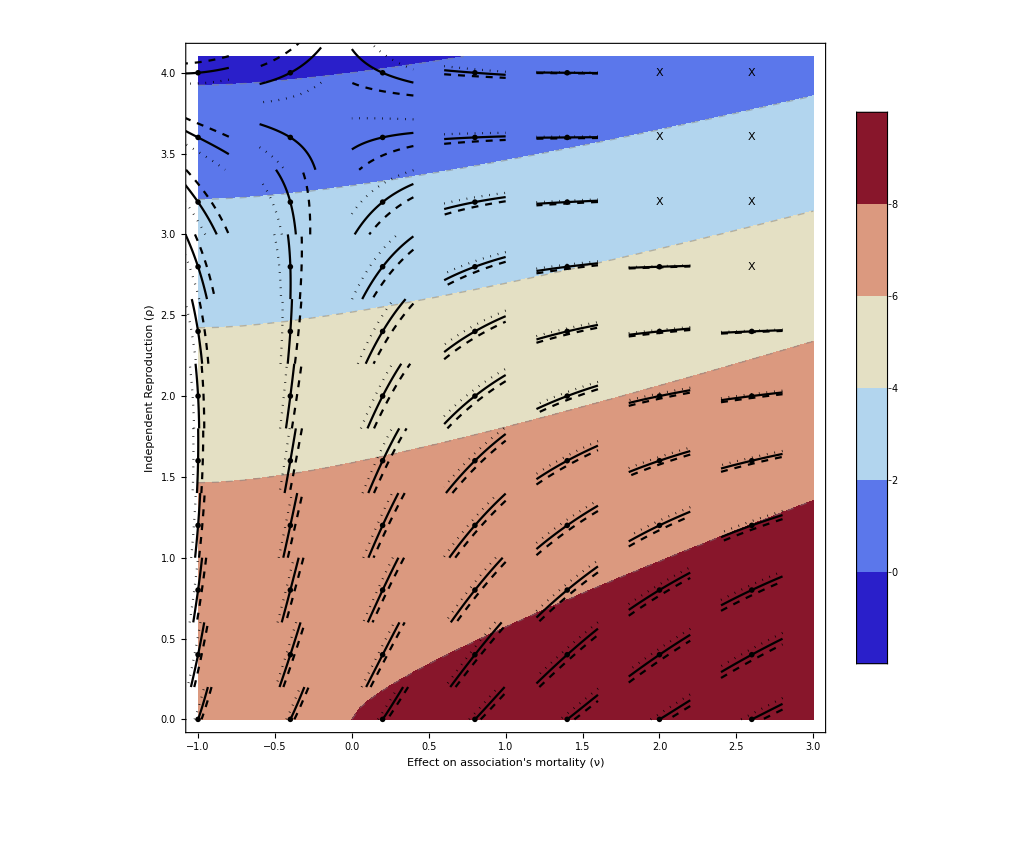

```mathematica
Show[ContourPlot[𝒪/.par2, {ν, νrange[[1]], νrange[[2]]}, {ρ, ρrange[[1]], ρrange[[2]]},Frame-> True, FrameLabel->{ "Effect on association's mortality (ν)","Independent Reproduction (ρ)"}, ColorFunction->"ThermometerColors",PlotLegends->Automatic, FrameStyle->frameStyle, LabelStyle->labelStyle, ContourStyle->Directive[Gray,Dashed]],MapThread[ContourPlot, {(ℐ-𝒪==0)/.par2/.par2eq, νlistContourRange, ρlistContourRange, ConstantArray[{ ContourStyle->Directive[Black]}, Length[νlistContourRange]]}],
MapThread[ContourPlot, {(ℐ-𝒪==0.1)/.par2/.par2eq, νlistContourRange, ρlistContourRange, ConstantArray[{ ContourStyle->Directive[Black, Dashed]}, Length[νlistContourRange]]}],
MapThread[ContourPlot, {(ℐ-𝒪==-0.1)/.par2/.par2eq, νlistContourRange, ρlistContourRange, ConstantArray[{ ContourStyle->Directive[Black, Dotted]}, Length[νlistContourRange]]}],ListPlot[par2νρ, PlotStyle->Black, PlotMarkers->"OpenMarkers"],ListPlot[par1νρextinct, PlotStyle->Black, PlotMarkers->"X"]]
```